```mathematica
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];
Off[General::spell1];
```

```mathematica
coords={t,r,θ,ϕ};
```

```mathematica
gdd={{g00,0,0,g03},{0,g11,0,0},{0,0,g22,0},{g03,0,0,g33}};
MatrixForm[gdd]
g00=-ⅇ^(2f0[r,θ]) H[r]+ⅇ^(2f2[r,θ]) r^2 Sin[θ]^2 W[r,θ]^2;
g03=-ⅇ^(2f2[r,θ])r^2 Sin[θ]^2 W[r,θ];
g11=ⅇ^(2f1[r,θ])/H[r];
g22=ⅇ^(2f1[r,θ]) r^2;
g33=ⅇ^(2f2[r,θ]) r^2 Sin[θ]^2;MatrixForm[gdd]
```

(g00 | 0 | 0 | g03
0 | g11 | 0 | 0
0 | 0 | g22 | 0
g03 | 0 | 0 | g33)

(-ⅇ^(2 f0[r,θ]) H[r]+ⅇ^(2 f2[r,θ]) r^2 Sin[θ]^2 W[r,θ]^2 | 0 | 0 | -ⅇ^(2 f2[r,θ]) r^2 Sin[θ]^2 W[r,θ]
0 | ⅇ^(2 f1[r,θ])/H[r] | 0 | 0
0 | 0 | ⅇ^(2 f1[r,θ]) r^2 | 0
-ⅇ^(2 f2[r,θ]) r^2 Sin[θ]^2 W[r,θ] | 0 | 0 | ⅇ^(2 f2[r,θ]) r^2 Sin[θ]^2)

```mathematica
guu=Inverse[gdd];
dim=Length[gdd];
```

```mathematica
Do[g[i,j]=Simplify[gdd[[i,j]]];,{i,1,dim},{j,1,dim}];
Do[gu[i,j]=Simplify[guu[[i,j]]];,{i,1,dim},{j,1,dim}];
```

```mathematica
DET=Simplify[Det[gdd]];
```

```mathematica
edd={{e00,0,0,e03},{0,e11,0,0},{0,0,e22,0},{e30,0,0,e33}};
```

```mathematica
(*we=0;*)(*Static observer*)
we=-g03/g33;(*Zero angular momentum observer*)
(*we=a/(r^2+a^2);*)(*Carter observer*)
(*we=Sqrt[M]/(r^(3/2)+Sqrt[M]a)*)(*Freely orbiting stationary observer*)
ut=1/Sqrt[-g00-2 g03 we-g33 we^2];
e00=ut;
e03=ut we;
e11=Sqrt[gu[2,2]];
e22=Sqrt[gu[3,3]];
e30=-Sqrt[ut^2+gu[1,1]];
e33=Sqrt[ut^2 we^2+gu[4,4]];
euu=Simplify[Inverse[edd],Csc[θ]>0&&r>0&&f2[r,θ]>0&&f1[r,θ]>0&&f0[r,θ]>0&&H[r]>0];
dim=Length[gdd];
```

```mathematica
Do[e[i,j]=edd[[i,j]];,{i,1,dim},{j,1,dim}];
```

```mathematica
Do[eu[i,j]=euu[[i,j]];,{i,1,dim},{j,1,dim}];
```

```mathematica
MatrixForm[euu]
```

(ⅇ^f0[r,θ] √H[r] | 0 | 0 | -ⅇ^f2[r,θ] r Sin[θ] W[r,θ]
0 | ⅇ^f1[r,θ]/(√H[r]) | 0 | 0
0 | 0 | ⅇ^f1[r,θ] r | 0
0 | 0 | 0 | ⅇ^f2[r,θ] r Sin[θ])

```mathematica
(* A_μ *)
A = {At[r,θ]-Aphi[r,θ] Sin[θ] W[r,θ]/r^2,0,0,Aphi[r,θ]Sin[θ]};
MatrixForm[A]
```

(At[r,θ]-(Aphi[r,θ] Sin[θ] W[r,θ])/r^2
0
0
Aphi[r,θ] Sin[θ])

```mathematica
(* F_μν = d_μ A_ν - d_ν A_μ *)
F = Table[D[A[[ν]],coords[[μ]]] - D[A[[μ]],coords[[ν]]],{μ,1,dim},{ν,1,dim}];
MatrixForm[F];
```

```mathematica
(* F_ab = F_μν e_a^μ e_b^ν *)
tetradF = Simplify[Table[Sum[F[[μ,ν]]euu[[b,μ]]euu[[c,ν]],{μ,1,dim},{ν,1,dim}],{b,1,dim},{c,1,dim}],Sin[θ]>0];
MatrixForm[tetradF];
```

```mathematica
e1[r_,θ_]=Simplify[Re[tetradF[[1,2]]]];
e2[r_,θ_]=Simplify[Re[tetradF[[1,3]]]];
e3[r_,θ_]=Simplify[Re[tetradF[[1,4]]]];
b1[r_,θ_]=Simplify[Re[tetradF[[4,3]]]];
b2[r_,θ_]=Simplify[Re[tetradF[[2,4]]]];
b3[r_,θ_]=Simplify[Re[tetradF[[3,2]]]];
```

```mathematica
H[r_]:=1-rh/r;
```

```mathematica
dat=ReadList["funct.dat",Number,RecordLists->True];
nx=251;ny=30;
xmax=dat[[251,1]];xmin=dat[[1,1]];
ymax=dat[[nx*ny,2]];ymin=dat[[1,2]];
```

```mathematica
rh=0.05;
V=0.3;
```

```mathematica
Xtor[X_]:=If[X≠1,Sqrt[(X/(1-X))^2+rh^2],1000]
```

```mathematica
f1=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,3]]},{i,1,ny},{j,1,nx}];
f2=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,4]]},{i,1,ny},{j,1,nx}];
f0=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,5]]},{i,1,ny},{j,1,nx}];
W=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,6]]},{i,1,ny},{j,1,nx}];
Z=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,7]]},{i,1,ny},{j,1,nx}];
Aphi=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,8]]},{i,1,ny},{j,1,nx}];
At=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,9]]},{i,1,ny},{j,1,nx}];
```

```mathematica
if1=Interpolation[Flatten[f1,1],InterpolationOrder->4];
if2=Interpolation[Flatten[f2,1],InterpolationOrder->4];
if0=Interpolation[Flatten[f0,1],InterpolationOrder->4];
iW=Interpolation[Flatten[W,1],InterpolationOrder->4];
iZ=Interpolation[Flatten[Z,1],InterpolationOrder->4];
iAphi=Interpolation[Flatten[Aphi,1],InterpolationOrder->4];
iAt=Interpolation[Flatten[At,1],InterpolationOrder->4];
```

```mathematica
f1=if1;
f2=if2;
f0=if0;
W=iW;
Z=iZ;
Aphi=iAphi;
At=iAt;
```

```mathematica
r=.;θ=.;ϕ=.;x=.;y=.;z=.;
x[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ]
y[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ]
z[r_,θ_,ϕ_]:=r Cos[θ]
ϕ=π/2;
```

```mathematica
ex[r_,θ_,ϕ_]:=e1[r,θ] Sin[θ] Cos[ϕ]+e2[r,θ] Cos[θ] Cos[ϕ]-e3[r,θ] Sin[ϕ]
ey[r_,θ_,ϕ_]:=e1[r,θ] Sin[θ] Sin[ϕ]+e2[r,θ] Cos[θ] Sin[ϕ]+e3[r,θ] Cos[ϕ]
ez[r_,θ_,ϕ_]:=e1[r,θ] Cos[θ]-e2[r,θ] Sin[θ]
```

```mathematica
bx[r_,θ_,ϕ_]:=b1[r,θ] Sin[θ] Cos[ϕ]+b2[r,θ] Cos[θ] Cos[ϕ]-b3[r,θ] Sin[ϕ]
by[r_,θ_,ϕ_]:=b1[r,θ] Sin[θ] Sin[ϕ]+b2[r,θ] Cos[θ] Sin[ϕ]+b3[r,θ] Cos[ϕ]
bz[r_,θ_,ϕ_]:=b1[r,θ] Cos[θ]-b2[r,θ] Sin[θ]
```

```mathematica
rMin=5rh;
rMax=150;
```

```mathematica
ϕ=π/2;θ=.;
```

```mathematica
YZey=Interpolation[Flatten[Table[{y[r,θ,ϕ],z[r,θ,ϕ],ey[r,θ,ϕ]},{r,rMin,rMax,0.1},{θ,0,π/2,π/16}],1],InterpolationOrder->1];
YZez=Interpolation[Flatten[Table[{y[r,θ,ϕ],z[r,θ,ϕ],ez[r,θ,ϕ]},{r,rMin,rMax,0.1},{θ,0,π/2,π/16}],1],InterpolationOrder->1];
```

```mathematica
YZby=Interpolation[Flatten[Table[{y[r,θ,ϕ],z[r,θ,ϕ],by[r,θ,ϕ]},{r,rMin,rMax,0.1},{θ,0,π/2,π/16}],1],InterpolationOrder->1];
YZbz=Interpolation[Flatten[Table[{y[r,θ,ϕ],z[r,θ,ϕ],bz[r,θ,ϕ]},{r,rMin,rMax,0.1},{θ,0,π/2,π/16}],1],InterpolationOrder->1];
```

```mathematica
YZePlot=StreamPlot[{YZey[y,z],YZez[y,z]},{y,rMin,rMax},{z,rMin,rMax},VectorPoints->5];
YZbPlot=StreamPlot[{YZby[y,z],YZbz[y,z]},{y,rMin,rMax},{z,rMin,rMax},VectorPoints->5];
```

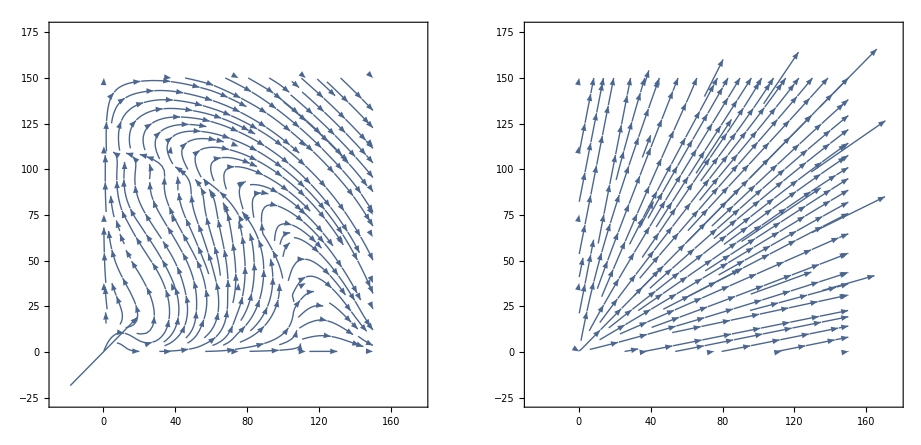

```mathematica
GraphicsRow[{YZePlot,YZbPlot}]
```

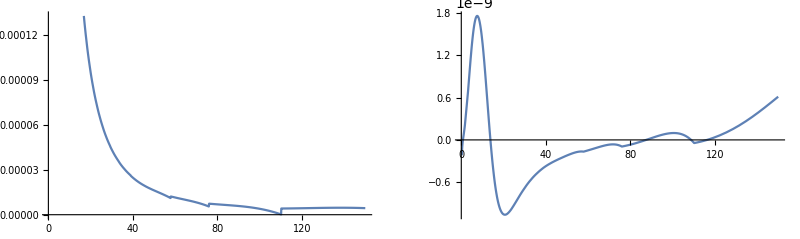

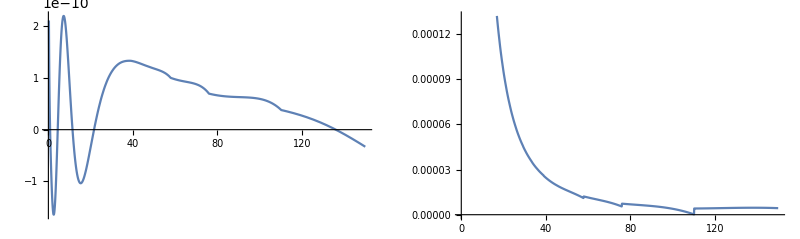

```mathematica
zInitial=0;yInitial=0;
GraphicsRow[{Plot[YZey[y,zInitial],{y,rMin,rMax}],Plot[YZez[y,zInitial],{y,rMin,rMax}]}]
GraphicsRow[{Plot[YZey[yInitial,z],{z,rMin,rMax}],Plot[YZez[yInitial,z],{z,rMin,rMax}]}]
```

```mathematica
YZeVPlot=VectorPlot[{YZey[y,z],YZez[y,z]},{y,rMin,rMax},{z,rMin,rMax},VectorPoints->Fine,VectorScale->{Small,0.6,Automatic}];
YZbVPlot=VectorPlot[{YZby[y,z],YZbz[y,z]},{y,rMin,rMax},{z,rMin,rMax},VectorPoints->Fine,VectorScale->{Small,0.6,Automatic}];
```

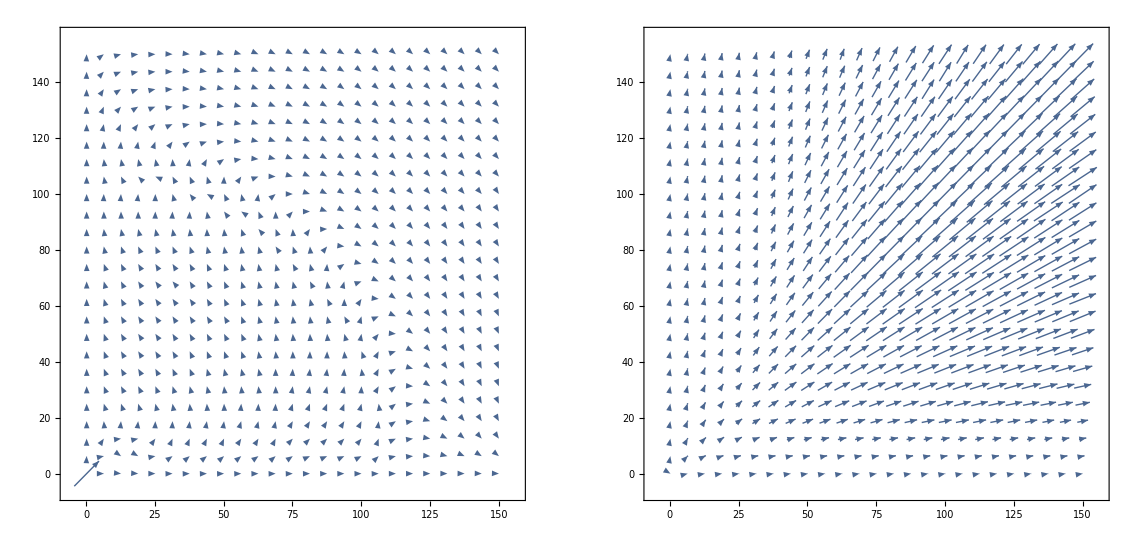

```mathematica
GraphicsRow[{YZeVPlot,YZbVPlot}]
```

```mathematica
θ=π/2;ϕ=.;
```

```mathematica
XYex=Interpolation[DeleteDuplicates[Flatten[Table[{x[r,θ,ϕ],y[r,θ,ϕ],ex[r,θ,ϕ]},{r,rMin,rMax,0.1},{ϕ,0,2 π,π/8}],1]],InterpolationOrder->1];
XYey=Interpolation[DeleteDuplicates[Flatten[Table[{x[r,θ,ϕ],y[r,θ,ϕ],ey[r,θ,ϕ]},{r,rMin,rMax,0.1},{ϕ,0,2 π,π/8}],1]],InterpolationOrder->1];
```

```mathematica
XYbx=Interpolation[DeleteDuplicates[Flatten[Table[{x[r,θ,ϕ],y[r,θ,ϕ],bx[r,θ,ϕ]},{r,rMin,rMax,0.1},{ϕ,0,2 π,π/8}],1]],InterpolationOrder->1];
XYby=Interpolation[DeleteDuplicates[Flatten[Table[{x[r,θ,ϕ],y[r,θ,ϕ],by[r,θ,ϕ]},{r,rMin,rMax,0.1},{ϕ,0,2 π,π/8}],1]],InterpolationOrder->1];
```

```mathematica
XYePlot=StreamPlot[{XYex[x,y],XYey[x,y]},{x,rMin,rMax},{y,rMin,rMax},VectorPoints->5];
XYbPlot=StreamPlot[{XYbx[x,y],XYby[x,y]},{x,rMin,rMax},{y,rMin,rMax},VectorPoints->5];
```

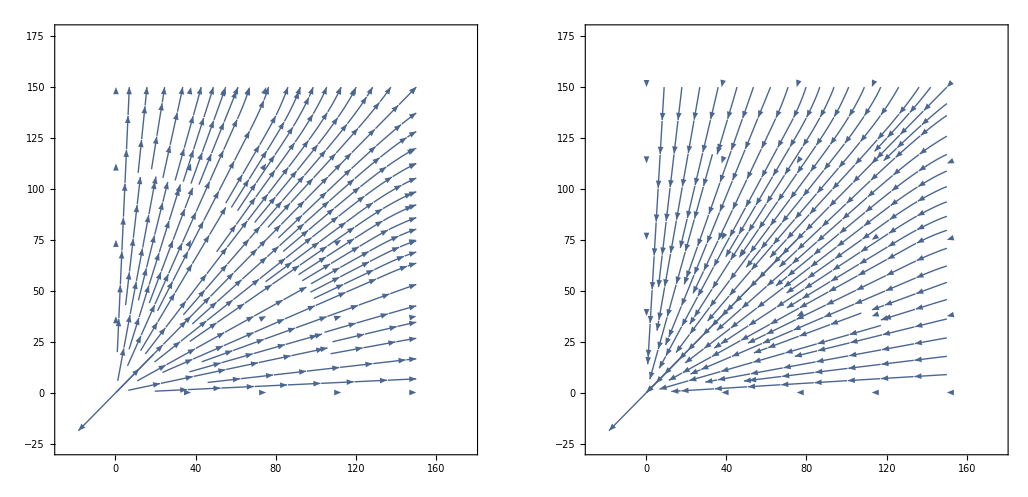

```mathematica
GraphicsRow[{XYePlot,XYbPlot}]
```

```mathematica
XYeVPlot=VectorPlot[{XYex[x,y],XYey[x,y]},{x,rMin,rMax},{y,rMin,rMax},VectorPoints->Fine,VectorScale->{Small,0.6,Automatic}];
XYbVPlot=VectorPlot[{XYbx[x,y],XYby[x,y]},{x,rMin,rMax},{y,rMin,rMax},VectorPoints->Fine,VectorScale->{Small,0.6,Automatic}];
```

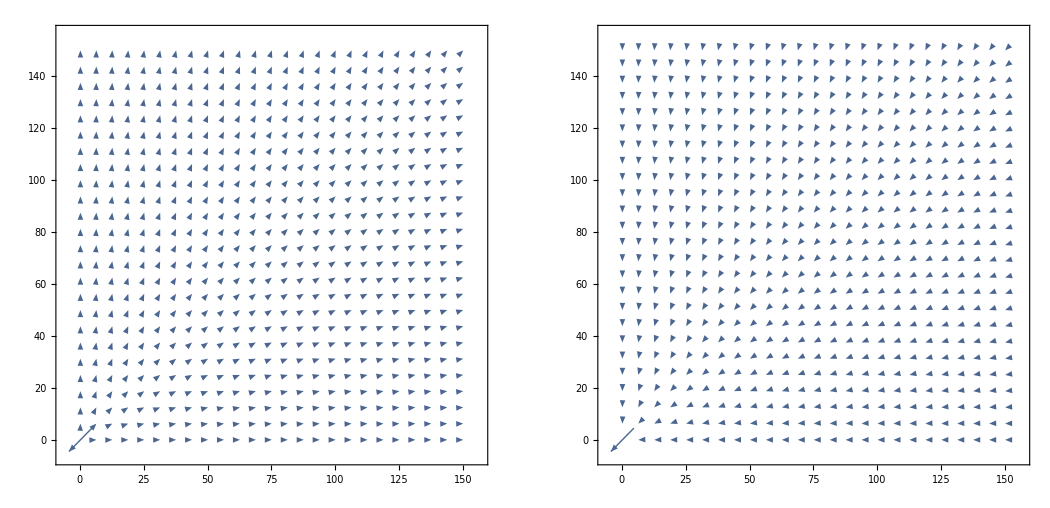

```mathematica
GraphicsRow[{XYeVPlot,XYbVPlot}]
```

```mathematica
Plot3D[XYex[x,y],{x,rMin,rMax},{y,rMin,rMax}]
Plot3D[XYey[x,y],{x,rMin,rMax},{y,rMin,rMax}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

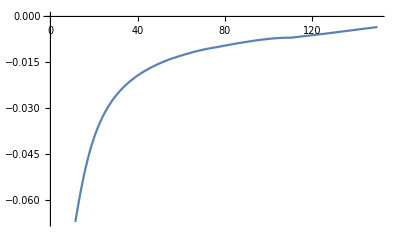

```mathematica
Plot[f0[r,π/2],{r,rh,rMax}]
```

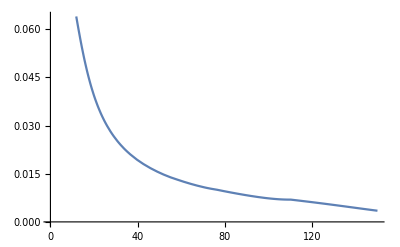

```mathematica
Plot[f1[r,π/2],{r,rh,rMax}]
```

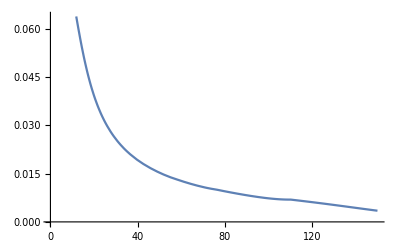

```mathematica
Plot[f2[r,π/2],{r,rh,rMax}]
```

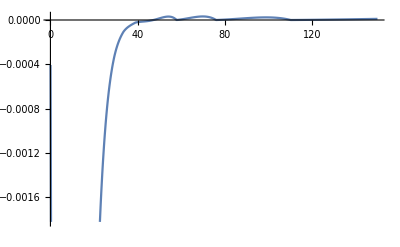

```mathematica
Plot[W[r,π/2],{r,rh,rMax}]
```

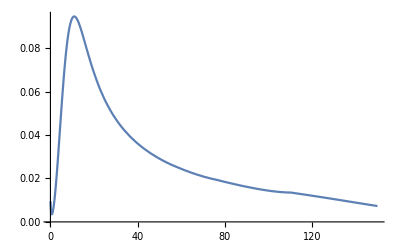

```mathematica
Plot[Z[r,π/2],{r,rh,rMax}]
```

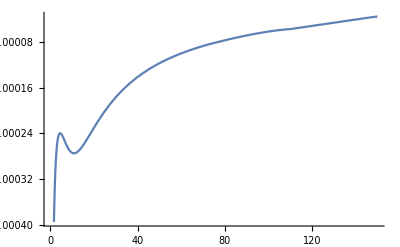

```mathematica
Plot[Aphi[r,π/2],{r,rh,rMax}]
```

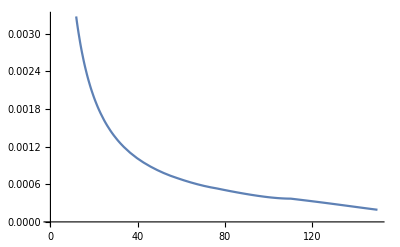

```mathematica
Plot[At[r,π/2],{r,rh,rMax}]
```

```mathematica
rr[r_] = g11/.r-> r;
tt[r_] = g00/.r-> r;
θθ[r_] = g22/.r-> r;
ϕϕ[r_] = g33/.r-> r;
tϕ[r_] = g03/.r-> r;
```

```mathematica
θ=π/2;
```

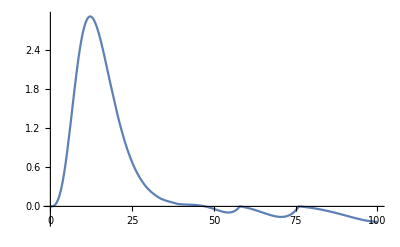

```mathematica
Plot[tϕ[r],{r,rh,100}]
```

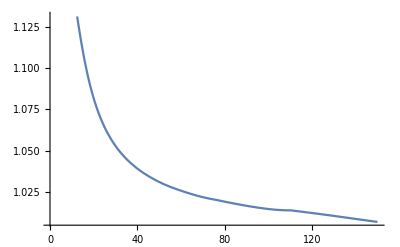

```mathematica
Plot[Exp[2 f2[r,π/2]],{r,rMin,rMax}]
```

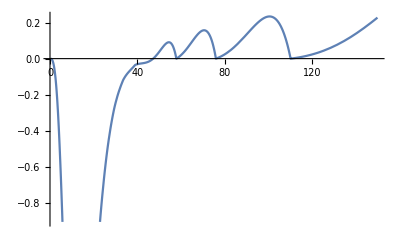

```mathematica
Plot[r^2 W[r,π/2],{r,rMin,rMax}]
```